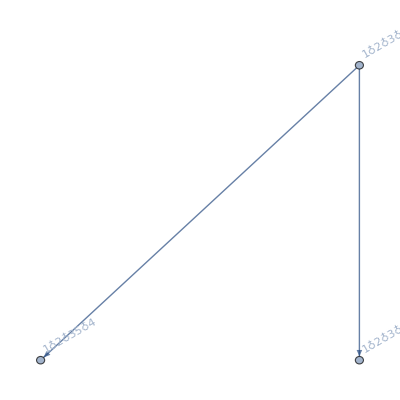
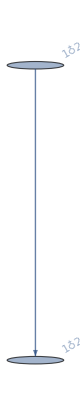
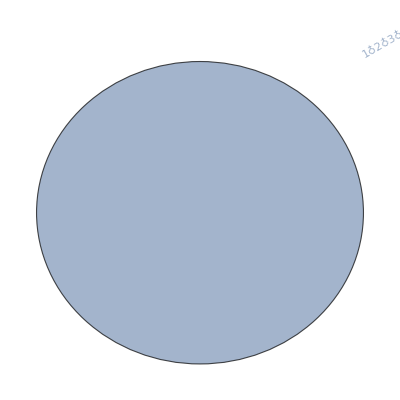
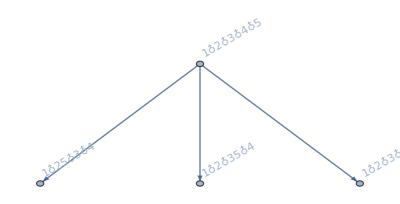
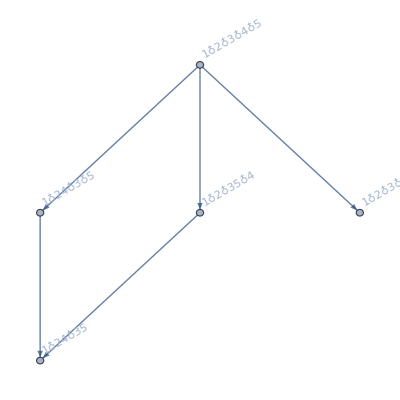
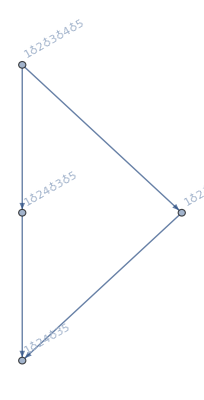
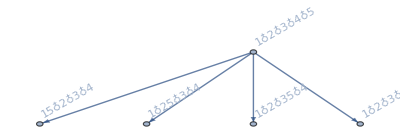
{{-Graphics-295200,30,-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-},{-Graphics-295230,10,-Graphics-295250+-Graphics-295240,-Graphics-},{-Graphics-295240,1,-Graphics-295240,-Graphics-},{-Graphics-294930,20,-Graphics-295510+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-},{-Graphics-294390,15,-Graphics-296080+-Graphics-296050+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-},{-Graphics-294400,5,-Graphics-296080+-Graphics-296050+-Graphics-295270+-Graphics-295240,-Graphics-},{-Graphics-287640,5,-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-}}

```mathematica
Map[{ShowGraph5Least[#[[1]]],#[[2]],(allGraphs5[#[[1]],"colofour"]/.RepGraph["C"]),FormulaGraphReverse2[allGraphs5[#[[1]],"colofour"]]}&,Tally[Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&&allGraphs5[#,"atleast"]==0]&],IsomorphicGraphQ[allGraphs5[#1,"graph"],allGraphs5[#2,"graph"]]&]]
```

```mathematica
Map[{ShowGraph5Least[#[[1]]],#[[2]],Map[SymbolToLabel,ListofVars[allGraphs5[#[[1]],"colofourgenerator"]]]}&,Tally[Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&&allGraphs5[#,"atleast"]==0]&],IsomorphicGraphQ[allGraphs5[#1,"graph"],allGraphs5[#2,"graph"]]&]]
```

{{-Graphics-295200,30,{1♁2♁35♁4,1♁2♁3♁45,1♁2♁3♁4♁5}},{-Graphics-295230,10,{1♁2♁3♁45}},{-Graphics-295240,1,{1♁2♁3♁4♁5}},{-Graphics-294930,20,{1♁25♁3♁4,1♁2♁35♁4,1♁2♁3♁45,1♁2♁3♁4♁5}},{-Graphics-294390,15,{1♁24♁35,1♁2♁3♁45,1♁2♁3♁4♁5}},{-Graphics-294400,5,{1♁24♁35}},{-Graphics-287640,5,{15♁2♁3♁4,1♁25♁3♁4,1♁2♁35♁4,1♁2♁3♁45,1♁2♁3♁4♁5}}}

```mathematica
Map[ShowGraph5Least,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&&allGraphs5[#,"atleast"]==0]&]]
```

{-Graphics-295200,-Graphics-295230,-Graphics-295240,-Graphics-295210,-Graphics-295140,-Graphics-295150,-Graphics-295120,-Graphics-294930,-Graphics-294960,-Graphics-294970,-Graphics-294940,-Graphics-294390,-Graphics-294420,-Graphics-294430,-Graphics-294400,-Graphics-294330,-Graphics-294340,-Graphics-294310,-Graphics-294160,-Graphics-292810,-Graphics-292780,-Graphics-292720,-Graphics-292690,-Graphics-292540,-Graphics-292000,-Graphics-291970,-Graphics-291730,-Graphics-287910,-Graphics-287940,-Graphics-287950,-Graphics-287920,-Graphics-287640,-Graphics-287670,-Graphics-287680,-Graphics-287650,-Graphics-273330,-Graphics-273360,-Graphics-273370,-Graphics-273340,-Graphics-273270,-Graphics-273280,-Graphics-273250,-Graphics-273090,-Graphics-273100,-Graphics-272550,-Graphics-272560,-Graphics-272460,-Graphics-272470,-Graphics-266080,-Graphics-266050,-Graphics-265810,-Graphics-229630,-Graphics-229600,-Graphics-229540,-Graphics-229510,-Graphics-229360,-Graphics-228820,-Graphics-228730,-Graphics-227200,-Graphics-227170,-Graphics-227110,-Graphics-227080,-Graphics-226930,-Graphics-226390,-Graphics-222340,-Graphics-222070,-Graphics-207760,-Graphics-200470,-Graphics-98410,-Graphics-98140,-Graphics-97600,-Graphics-97330,-Graphics-95980,-Graphics-95710,-Graphics-95170,-Graphics-94900,-Graphics-91120,-Graphics-76540,-Graphics-76270,-Graphics-69250,-Graphics-32800,-Graphics-32530,-Graphics-31990,-Graphics-25510,-Graphics-10930,-Graphics-3640}